```mathematica
Clear[Vleps,qAB,qBC,qAC,jAB,jBC,jAC]
dAB=4.746 ;            (* the well depth in eV of the AB interaction *)
dBC=4.746 ;            (*      -                      BC      -      *)
dAC=3.445 ;            (*      -                      AC      -      *)
r0AB=0.742 ;         (* the bond distance in Angstrom for the AB dimer *)
r0BC=0.742 ;         (*            -                          BC   -   *)
r0AC=0.742 ;          (*            -                          AC   -   *)
alphaAB=1.942 ;   (* the exponential decay length of AB interaction *)
alphaBC=1.942 ;  (*         -                       BC      -      *)
alphaAC=1.942 ;  (*         -                       AC      -      *)
ap1=1.05 ;               (* This is written as (1+a) in the lecture notes *)
bp1=1.30 ;               (*        -           (1+b)          -           *) 
cp1=1.05;                (*        -           (1+c)          -           *)

qAB[r_] =  dAB/4 (3 Exp[-2 alphaAB (r-r0AB)] - 2 Exp[- alphaAB (r-r0AB)]);
qBC[r_] =  dBC/4 (3 Exp[-2 alphaBC (r-r0BC)] - 2 Exp[- alphaBC (r-r0BC)]);
qAC[r_] =  dAC/4 (3 Exp[-2 alphaAC (r-r0AC)] - 2 Exp[- alphaAC (r-r0AC)]);

jAB[r_] =  dAB/4 (Exp[-2 alphaAB (r-r0AB)] - 6 Exp[- alphaAB (r-r0AB)]);
jBC[r_] =  dBC/4 (Exp[-2 alphaBC (r-r0BC)] - 6 Exp[- alphaBC (r-r0BC)]);
jAC[r_] =  dAC/4 (Exp[-2 alphaAC (r-r0AC)] - 6 Exp[- alphaAC (r-r0AC)]);

Vleps[rab_,rbc_] =  qAB[rab]/ap1 + qBC[rbc]/bp1 + qAC[rab+rbc]/cp1 -
                   Sqrt[(jAB[rab]/ap1)^2 + (jBC[rbc]/bp1)^2 + (jAC[rab+rbc]/cp1)^2 -
                         jAB[rab] jBC[rbc]/(ap1 bp1) - jBC[r2] jAC[rab+rbc]/(bp1 cp1)-
                         jAB[rab] jAC[rab+rbc] /(ap1 cp1)] ;
Vleps[r1,r2]
```

1.13 (3 ⅇ^(-3.884 (-0.742+r1))-2 ⅇ^(-1.942 (-0.742+r1)))+0.912692 (3 ⅇ^(-3.884 (-0.742+r2))-2 ⅇ^(-1.942 (-0.742+r2)))+0.820238 (3 ⅇ^(-3.884 (-0.742+r1+r2))-2 ⅇ^(-1.942 (-0.742+r1+r2)))-√(1.2769 (ⅇ^(-3.884 (-0.742+r1))-6 ⅇ^(-1.942 (-0.742+r1)))^2-1.03134 (ⅇ^(-3.884 (-0.742+r1))-6 ⅇ^(-1.942 (-0.742+r1))) (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2)))+0.833007 (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2)))^2-0.926869 (ⅇ^(-3.884 (-0.742+r1))-6 ⅇ^(-1.942 (-0.742+r1))) (ⅇ^(-3.884 (-0.742+r1+r2))-6 ⅇ^(-1.942 (-0.742+r1+r2)))-0.748625 (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2))) (ⅇ^(-3.884 (-0.742+r1+r2))-6 ⅇ^(-1.942 (-0.742+r1+r2)))+0.672791 (ⅇ^(-3.884 (-0.742+r1+r2))-6 ⅇ^(-1.942 (-0.742+r1+r2)))^2)

```mathematica
Vleps[rab,rbc]
```

1.13 (3 ⅇ^(-3.884 (-0.742+rab))-2 ⅇ^(-1.942 (-0.742+rab)))+0.912692 (3 ⅇ^(-3.884 (-0.742+rbc))-2 ⅇ^(-1.942 (-0.742+rbc)))+0.820238 (3 ⅇ^(-3.884 (-0.742+rab+rbc))-2 ⅇ^(-1.942 (-0.742+rab+rbc)))-√(1.2769 (ⅇ^(-3.884 (-0.742+rab))-6 ⅇ^(-1.942 (-0.742+rab)))^2-1.03134 (ⅇ^(-3.884 (-0.742+rab))-6 ⅇ^(-1.942 (-0.742+rab))) (ⅇ^(-3.884 (-0.742+rbc))-6 ⅇ^(-1.942 (-0.742+rbc)))+0.833007 (ⅇ^(-3.884 (-0.742+rbc))-6 ⅇ^(-1.942 (-0.742+rbc)))^2-0.748625 (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2))) (ⅇ^(-3.884 (-0.742+rab+rbc))-6 ⅇ^(-1.942 (-0.742+rab+rbc)))-0.926869 (ⅇ^(-3.884 (-0.742+rab))-6 ⅇ^(-1.942 (-0.742+rab))) (ⅇ^(-3.884 (-0.742+rab+rbc))-6 ⅇ^(-1.942 (-0.742+rab+rbc)))+0.672791 (ⅇ^(-3.884 (-0.742+rab+rbc))-6 ⅇ^(-1.942 (-0.742+rab+rbc)))^2)

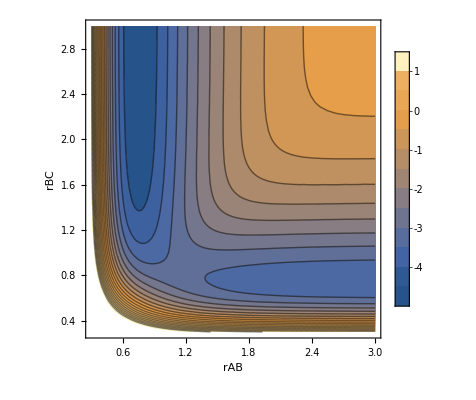

```mathematica
rMin=0.3;
rMax=3.0;
ContourPlot[Vleps[r1,r2],{r1,rMin,rMax},{r2,rMin,rMax},Contours->20,PlotLegends->{-4.5,-4,-3.5,-3,-2.5,-2,-1.5,-1,-.5,0,.5,1.0},FrameLabel->{"rAB","rBC"}]
```

```mathematica
rMin=0.3;
rMax=3.0;
ContourPlot[Vleps[rab,rbc],{rab,rMin,rMax},{rbc,rMin,rMax},Contours->20,PlotLegends->{-4.5,-4,-3.5,-3,-2.5,-2,-1.5,-1,-.5,0,.5,1.0},FrameLabel->{"rAB","rBC"}]
```

-Graphics-

```mathematica
rMin=0.3;
rMax=3.0;
ContourPlot[Vleps[r1,r2],{r1,rMin,rMax},{r2,rMin,rMax},Contours->20,PlotLegends->{-4.5,-4,-3.5,-3,-2.5,-2,-1.5,-1,-.5,0,.5,1.0},FrameLabel->{"rAB","rBC"}]
```

-Graphics-

The difference between the LEPS potential surface and the L-J potential surface is that the bottom right portion of the graph is no longer the region of minimized potential. In this LEPS plot, there are two bands - one vertical and one horizontal - where the potential is minimized instead.